## C1: Solution Using a Numerical Solver

```mathematica
Unprotect[C];
Clear[A,B,C,k1,k2,k1b,k2b];

(*Let c represent C. It doesn't work with C even after unprotecting (? - not sure why, since it worked for previous problems).*)

EqnSeqB={
A'[t]==-k1 A[t] + k1b B[t],
B'[t]==k1 A[t]-k1b B[t]-k2 B[t]+k2b c[t],
c'[t]==k2 B[t]-k2b c[t],
A[0]==A0,
B[0]==B0,
c[0]==c0
};
subND = {A0->1,B0->0,c0->0,k1->1,k1b->0.05,k2->0.1,k2b->0.1};
SolSeqB=NDSolve[EqnSeqB/.subND,{A[t],B[t],c[t]},{t,0,100000}][[1]]
```

{A[t]→InterpolatingFunction[…][t],B[t]→InterpolatingFunction[…][t],c[t]→InterpolatingFunction[…][t]}

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

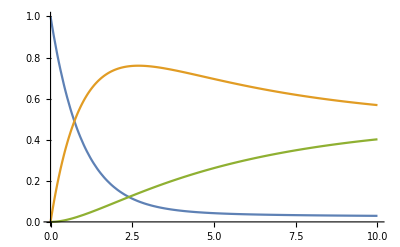

```mathematica
A[t_]=A[t]/.SolSeqB
B[t_]=B[t]/.SolSeqB
c[t_]=c[t]/.SolSeqB
Plot[{A[t],B[t],c[t]},{t,0,10}]


(*common error: the graph didn't show up at first because i forgot to define actual functions that use the obtained solutions as subsitutions.*)
```

## C2: Solution Using Euler’s Method

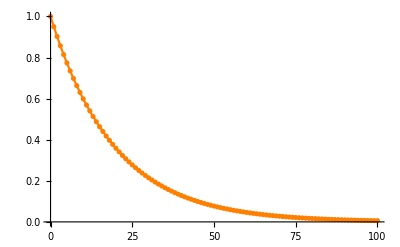

Concentration at t=100 using h=1: 0.00592053

```mathematica
A0n=1.0;
kn=0.05;
time=100;
h=1;
nSteps=Round[time/h];
An[0]=A0n;

For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h kn An[n];
];

AData=Table[{n h,An[n]},{n,0,nSteps}];

plot1=ListPlot[AData,PlotRange->{0,1},Joined->True,Mesh->All,PlotStyle->{Orange}]

(*The variable below is the numerical prediction of concentration at t=100 using h=1*)
concPrediction1 = An[Round[100/h]];

Print["Concentration at t=100 using h=1: ",concPrediction1]
```

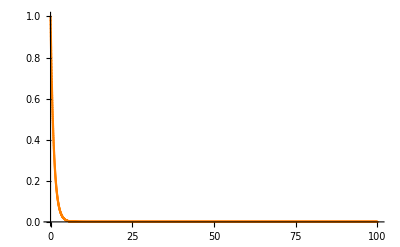

Concentration at t=100 using h=1: 1.49518×10^-44

```mathematica
A0n=1.0;
kn=0.05;
time=100;
h=0.02;
nSteps=Round[time/h];
An[0]=A0n;

For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h(An[n]-h kn An[n]);
]

AData=Table[{n h,An[n]},{n,0,nSteps}];

plot1=ListPlot[AData,PlotRange->{0,1},Joined->True,Mesh->All,PlotStyle->{Orange}]

(*The variable below is the numerical prediction of concentration at t=100 using h=1*)
concPrediction1 = An[Round[100/h]];

Print["Concentration at t=100 using h=1: ",concPrediction1]
```

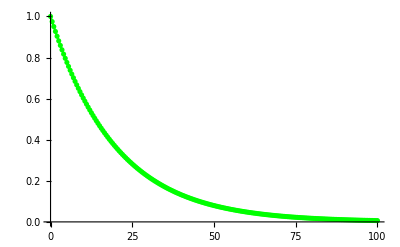

Concentration at t=100 using h=0.5: 0.006323

```mathematica
A0n=1.0;
kn=0.05;
time=100;
h=0.5;
nSteps=Round[time/h];
An[0]=A0n;

For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h kn An[n];
];

AData=Table[{n h,An[n]},{n,0,nSteps}];

plot2=ListPlot[AData,PlotRange->{0,1},Joined->True,Mesh->All, PlotStyle->{Green}]

(*The variable below is the numerical prediction of concentration at t=100 using h=0.5*)
concPredictionPoint5 = An[Round[100/h]];

Print["Concentration at t=100 using h=0.5: ",concPredictionPoint5]
```

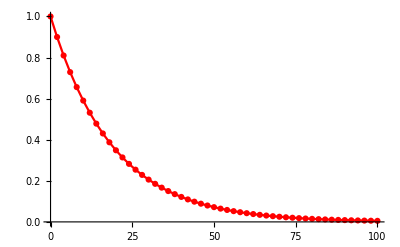

Concentration at t=100 using h=2: 0.00515378

```mathematica
A0n=1.0;
kn=0.05;
time=100;
h=2;
nSteps=Round[time/h];
An[0]=A0n;

For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h kn An[n];
];

AData=Table[{n h,An[n]},{n,0,nSteps}];

plot3=ListPlot[AData,PlotRange->{0,1},Joined->True,Mesh->All,PlotStyle->{Red}]

(*The variable below is the numerical prediction of concentration at t=100 using h=2*)
concPrediction2=An[Round[100/h]];

Print["Concentration at t=100 using h=2: ",concPrediction2]
```

Combined Plot:

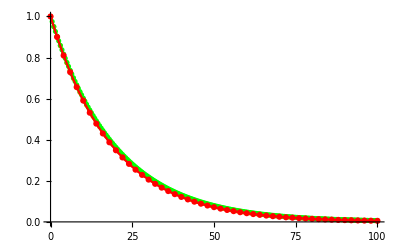

Zoomed in:

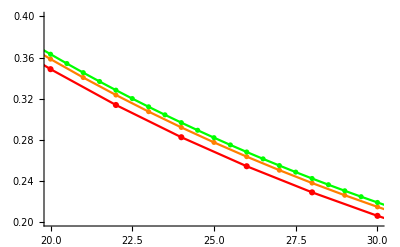

```mathematica
Print["Combined Plot:"]
Show[{plot1,plot2,plot3}]

Print["Zoomed in:"]
Show[{plot1,plot2,plot3},PlotRange->{{20,30},{0.2,0.4}}]
```

```mathematica
A0n=1.0;
kn=0.05;
time=100;
h=0.02;
nSteps=Round[time/h];
An[0]=A0n;

For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h kn An[n];
];

(*The variable below is the numerical prediction of concentration at t=100 using h=0.02*)
concPredictionPoint02=An[Round[100/h]];

Print["Concentration at t=100, using small step size of h=0.02: ",concPredictionPoint02]
```

Concentration at t=100, using small step size of h=0.02: 0.00672111

In the above plots, we have used a different step size for each, leading to different results for the estimated concentration at t=100. When using h=2 and h=1, the predictions were 0.00515 and 0.00592, respectively. When using h=0.5, the prediction sat higher at a value of 0.0063. When using an extremely small step size of h=0.02, the prediction was about 0.0067. Since we know that the estimation must be closer to the true value as step size decreases, we know that 0.0067 should be the most accurate and that the estimation is lower with increasing step size. Depending on how much error in the prediction we are willing to accept, our decision for what step size to use would differ. First, let us find the true value for the concentration at t=100 using the analytical solution, as shown below:

```mathematica
Eqn1={
A'[t]==-k A[t],
A[0]==A0
};
Sol1 = DSolve[Eqn1, A[t], t][[1]]
A1[t_]=A[t]/.Sol1
analyticalSolution = A1[100]/.{A0->1,k->0.05}
Print["The analytical solution predicts that the concentration at t=100 is ", analyticalSolution]
```

{A[t]→A0 ⅇ^(-k t)}

A0 ⅇ^(-k t)

0.00673795

The analytical solution predicts that the concentration at t=100 is 0.00673795

```mathematica
errorwith2 = analyticalSolution-concPrediction2;
errorwith1 = analyticalSolution-concPrediction1;
errorwithPoint5 = analyticalSolution-concPredictionPoint5;
errorwithPoint02 = analyticalSolution-concPredictionPoint02;

Print["error with h=2: ",errorwith2 ]
Print["error with h=1: ", errorwith1]
Print["error with h=0.5: ", errorwithPoint5]
Print["error with h=0.02: ", errorwithPoint02]

(*The above variables represent the difference between each numerical prediction using the differenct step sizes and the analytical prediction for concentration at t=100.*)
```

error with h=2: 0.00158417

error with h=1: 0.000817418

error with h=0.5: 0.000414948

error with h=0.02: 0.000016835

If we compare the analytical solution with each of the numerical solutions with different step sizes, we obtain the differences as listed above. When using h=.02, we had an extremely low error of .000016, which shows that a step size as small as possible is ideal to minimize error. However, the requirement for what step size we need to obtain a reasonable prediction may be much higher depending on how much error we are willing to accept. With h=0.5, there is more error compared to h=.02 but not by a large margin. If a difference of 0.00041 between the numerical prediction and analytical result is something that is acceptable, then h=0.5 is an acceptable step size to use. With larger step sizes such as h=1 and h=2, the error almost doubles from the previous step sizes and thus it is most likely not ideal to use such large step sizes. 

To fully grasp how the step size is related to the error in our prediction when compared to the analytical result for concentration at t=100, we can run the same numerical solution with several step sizes and create a regression model that relates step size with error. Obtaining a regression equation and a visualization of this relationship would be ideal to see the complete picture and make an informed decision about what step size is acceptable in a particular situation.

```mathematica
A0n=1.0;
kn=0.05;
time=100;
h=1;
nSteps=Round[time/h];
An[0]=A0n;

For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h kn An[n];
];

AData=Table[{n h,An[n]},{n,0,nSteps}];

plot1=ListPlot[AData,PlotRange->{0,1},Joined->True,Mesh->All,PlotStyle->{Orange}]
```

## C3: Sequential First Order Without Back Reactions

step size: 1

0.366032, 0.0192649, 0.614703

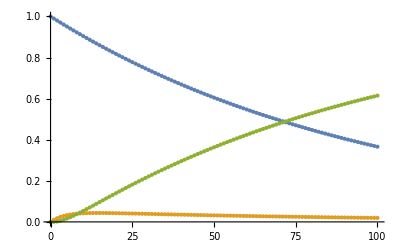

step size: 0.5

0.366958, 0.0193136, 0.613729

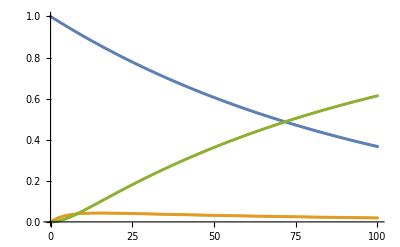

step size: 2

0.36417, 0.0191668, 0.616663

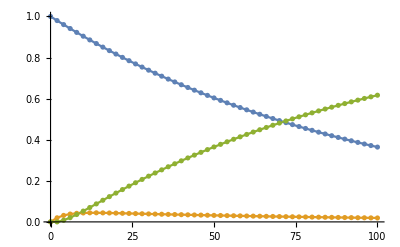

step size: 0.02

0.367843, 0.0193601, 0.612797

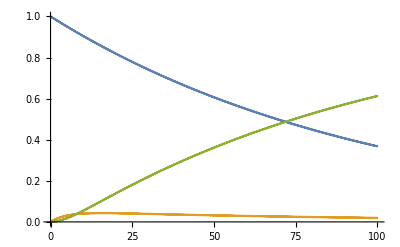

Combined plot:

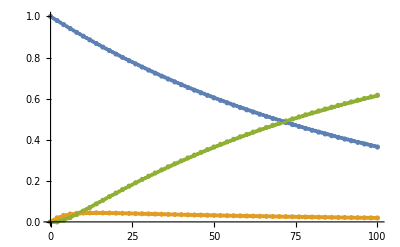

```mathematica
(*Note that the "i" in the variable names represents "input" to differentiate from the parameter names of the function defined for the Euler approximation.*)

Clear[A0i,B0i,C0i,k1i,k2i,time,hi,nStepsi,AData,BData,CData,AconcPrediction,BconcPrediction,CconcPrediction,An,Bn,Cn];
A0i=1.0;
B0i=0;
C0i=0;
k1i=0.01;(*A->B*)
k2i=0.2;(*B->C*)

time=100.0;
hi=1;
nStepsi=Round[time/hi];

An[0]=A0i;
Bn[0]=B0i;
Cn[0]=C0i;

def[A0_,B0_,C0_,h_,k1_,k2_,nSteps_]:=(
For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h k1 An[n];
Bn[n+1]=Bn[n]+h k1 An[n]-h k2 Bn[n];
Cn[n+1]=Cn[n]+h k2 Bn[n];
];
AData=Table[{n h,An[n]},{n,0,nSteps}];
BData=Table[{n h,Bn[n]},{n,0,nSteps}];
CData=Table[{n h,Cn[n]},{n,0,nSteps}];


AconcPrediction = An[Round[100/h]];
BconcPrediction = Bn[Round[100/h]];
CconcPrediction=Cn[Round[100/h]];
Print[AconcPrediction, ", ",BconcPrediction,", ",CconcPrediction];
)

Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,nStepsi];
plot1= ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]


hi=0.5;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,nStepsi];
plot2 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=2;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,nStepsi];
plot3=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.02;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,nStepsi];
plot4=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

Print["Combined plot: "]
Show[{plot1,plot2,plot3,plot4}]
```

So far what we have done is create a function that takes in the parameters and outputs the concentrations at t=100 along with the plot.
Now we must create a for loop that uses the halving function to assign 10 different values for h, outputting the concentrations at t=100 for each.

We could have used this approach for the previous section as well to make the code shorter.

Before the for loop, we need to consider the analytical solution and its prediction for concentrations at t=100 to compare with the different numerical predictions and see what the error or difference for each one was.

In the previous section, we copied and pasted the code from A1 of the first problem set for the analytical solution. For this section, we can use the code from B5 of the second problem set. 

However, note that in the previous section we got an concrete analytical solution just using A0=1. Here, we have to rely on the assumptions that A0=1, B0=0 and C0=0 to get an analytical solution.

```mathematica
Unprotect[C];
Clear[A,B,C,k1,k2,A0,B0,C0];
EqnSeqNB = {
A'[t]==-k1 A[t],
B'[t]==k1 A[t]-k2 B[t],
c'[t]==k2 B[t],
A[0]==A0,
B[0]==B0,
c[0]==c0
};

SolSeqNB = DSolve[EqnSeqNB,{A[t],B[t],c[t]},t][[1]];

AseqNB[t_]=A[t]/.Part[SolSeqNB,1]/.{A0->1,B0->0,c0->0,k1->0.01,k2->0.2};
BseqNB[t_]=B[t]/.Part[SolSeqNB,2]/.{A0->1,B0->0,c0->0,k1->0.01,k2->0.2};
CseqNB[t_]=c[t]/.Part[SolSeqNB,3]/.{A0->1,B0->0,c0->0,k1->0.01,k2->0.2};

analyticalSolA=AseqNB[100]
analyticalSolB=BseqNB[100]
analyticalSolC=CseqNB[100]
```

0.367879

0.0193621

0.612758

Now we must use a for loop to:
- assign different step sizes
- output the numerical predictions for each one
- calculate and output error (or difference) between the numerical prediction and analytical prediction for each of the numerical solutions obtained.

```mathematica
(*Instead of manually resetting the step size and calling the function each time, we can automate it with a for loop. 
For some reason though, I'm not able to output a listplot for each step size if I use the for loop, so this only gives the concentrations at t=100 for each step size.*)

halvingFunction[x_]=0.5^x;

For[i=0,i<=10,i++,

hi=halvingFunction[i];
nStepsi=Round[time/hi];

Print["step size: ",hi];

Print["Concentrations of A,B,C, respectively, at t=100: "];
def[A0i,B0i,C0i,hi,k1i,k2i,nStepsi];

Print["error in predicted concentrations of A,B,C, respectively: "];
Print[analyticalSolA-AconcPrediction,", ", analyticalSolB-BconcPrediction,", ",  analyticalSolC-CconcPrediction];

Print["\n"];
]
```

step size: 1.

Concentrations of A,B,C, respectively, at t=100:

0.366032, 0.0192649, 0.614703

error in predicted concentrations of A,B,C, respectively:

0.0018471, 0.0000972157, -0.00194432

step size: 0.5

Concentrations of A,B,C, respectively, at t=100:

0.366958, 0.0193136, 0.613729

error in predicted concentrations of A,B,C, respectively:

0.000921619, 0.0000485062, -0.000970126

step size: 0.25

Concentrations of A,B,C, respectively, at t=100:

0.367419, 0.0193378, 0.613243

error in predicted concentrations of A,B,C, respectively:

0.000460329, 0.0000242278, -0.000484557

step size: 0.125

Concentrations of A,B,C, respectively, at t=100:

0.367649, 0.01935, 0.613001

error in predicted concentrations of A,B,C, respectively:

0.000230044, 0.0000121076, -0.000242152

step size: 0.0625

Concentrations of A,B,C, respectively, at t=100:

0.367764, 0.019356, 0.61288

error in predicted concentrations of A,B,C, respectively:

0.000114992, 6.05221×10^-6, -0.000121044

step size: 0.03125

Concentrations of A,B,C, respectively, at t=100:

0.367822, 0.0193591, 0.612819

error in predicted concentrations of A,B,C, respectively:

0.0000574886, 3.02571×10^-6, -0.0000605144

step size: 0.015625

Concentrations of A,B,C, respectively, at t=100:

0.367851, 0.0193606, 0.612789

error in predicted concentrations of A,B,C, respectively:

0.0000287425, 1.51276×10^-6, -0.0000302552

step size: 0.0078125

Concentrations of A,B,C, respectively, at t=100:

0.367865, 0.0193613, 0.612774

error in predicted concentrations of A,B,C, respectively:

0.0000143708, 7.56354×10^-7, -0.0000151271

step size: 0.00390625

Concentrations of A,B,C, respectively, at t=100:

0.367872, 0.0193617, 0.612766

error in predicted concentrations of A,B,C, respectively:

7.18526×10^-6, 3.78171×10^-7, -7.56343×10^-6

step size: 0.00195313

Concentrations of A,B,C, respectively, at t=100:

0.367876, 0.0193619, 0.612762

error in predicted concentrations of A,B,C, respectively:

3.5926×10^-6, 1.89084×10^-7, -3.78169×10^-6

step size: 0.000976563

Concentrations of A,B,C, respectively, at t=100:

0.367878, 0.019362, 0.61276

error in predicted concentrations of A,B,C, respectively:

1.79629×10^-6, 9.45416×10^-8, -1.89084×10^-6

As we can see, the error in the numerical predictions when compared to the analytical predictions for concentrations at t=100 decreases as step size decreases. With the last few step sizes, the error is extremely low and the numerical prediction is almost exactly the same as the analytical.

If we consider the same question of which step size to use, that again depends on what error we are willing to accept. A step size of 0.03 would probably be a good choice, since the error is minimized to a good extent around that point.

We can repeat this whole process for the next section which includes back reactions. We will use code from B6 for the analytical solution.

## C4: Sequential Reversible Reactions

For all the different runs of numerical solutions in this section, the forward rate constants stay the same (k1=.01,k2=0.2). However, we will be doing multiple runs that involve different test values for the back reaction’s rate constants. For this first run below, we use k1b=0.005 and k2b=0.1.

step size: 1

0.411426, 0.20335, 0.385224

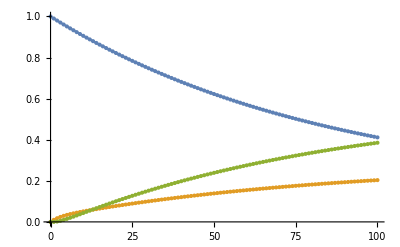

step size: 0.5

0.412331, 0.203072, 0.384597

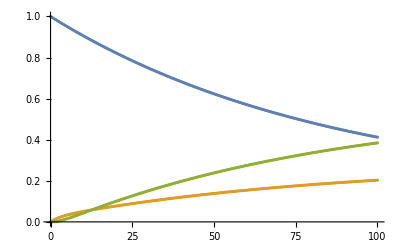

step size: 2

0.409604, 0.203909, 0.386488

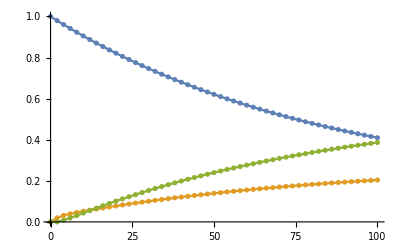

step size: 0.02

0.413196, 0.202807, 0.383997

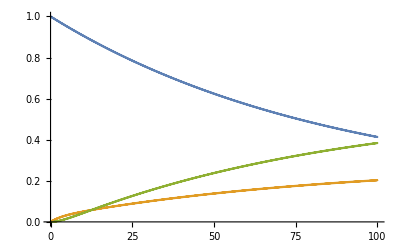

Combined plot:

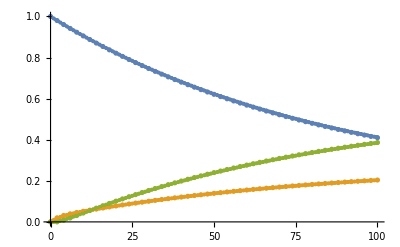

```mathematica
Clear[A0i,B0i,C0i,k1i,k2i,k1bi,k2bi,time,hi,nStepsi,AData,BData,CData,AconcPrediction,BconcPrediction,CconcPrediction,An,Bn,Cn];
A0i=1.0;
B0i=0;
C0i=0;
k1i=0.01;(*A->B*)
k2i=0.2;(*B->C*)
k1bi=0.005;
k2bi=0.1;


An[0]=A0i;
Bn[0]=B0i;
Cn[0]=C0i;

def[A0_,B0_,C0_,h_,k1_,k2_,k1b_,k2b_,nSteps_]:=(
For[n=0,n<=nSteps,n++,
An[n+1]=An[n]-h k1 An[n]+h k1b Bn[n];
Bn[n+1]=Bn[n]+h k1 An[n]-h k1b Bn[n]-h k2 Bn[n]+h k2b Cn[n];
Cn[n+1]=Cn[n]+h k2 Bn[n]-h k2b Cn[n];
];
AData=Table[{n h,An[n]},{n,0,nSteps}];
BData=Table[{n h,Bn[n]},{n,0,nSteps}];
CData=Table[{n h,Cn[n]},{n,0,nSteps}];


AconcPrediction = An[Round[100/h]];
BconcPrediction = Bn[Round[100/h]];
CconcPrediction=Cn[Round[100/h]];
Print[AconcPrediction, ", ",BconcPrediction,", ",CconcPrediction];
)


time=100.0;

hi=1;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot1= ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.5;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot2 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=2;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot3=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.02;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot4=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

Print["Combined plot: "]
Show[{plot1,plot2,plot3,plot4}]
```

```mathematica
Unprotect[C];
Clear[A,B,C,k1,k2,k1b,k2b,A0,B0,C0];
EqnSeqB={
A'[t]==-k1 A[t] + k1b B[t],
B'[t]==k1 A[t]-k1b B[t]-k2 B[t]+k2b c[t],
c'[t]==k2 B[t]-k2b c[t],
A[0]==A0,
B[0]==B0,
c[0]==c0
};

SolSeqB=DSolve[EqnSeqB,{A[t],B[t],c[t]},t][[1]];

k1bi
k2bi

AseqB[t_]=A[t]/.Part[SolSeqB,1]/.{A0->A0i,B0->B0i,c0->C0i,k1->k1i,k2->k2i};
BseqB[t_]=B[t]/.Part[SolSeqB,2]/.{A0->A0i,B0->B0i,c0->C0i,k1->k1i,k2->k2i};
CseqB[t_]=c[t]/.Part[SolSeqB,3]/.{A0->A0i,B0->B0i,c0->C0i,k1->k1i,k2->k2i};

(*the extra 'B' in the variable names is to differentiate from previous section, where 'B' represents 'back reaction'*)
analyticalSolAB= AseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolBB =BseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolCB =CseqB[100]/.{k1b->k1bi,k2b->k2bi}
```

0.005

0.1

0.413232

0.202796

0.383972

```mathematica
halvingFunction[x_]=0.5^x;

For[i=0,i<=10,i++,

hi=halvingFunction[i];
nStepsi=Round[time/hi];

Print["step size: ",hi];

Print["Concentrations of A,B,C, respectively, at t=100: "];
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];

Print["error in predicted concentrations of A,B,C, respectively: "];
Print[analyticalSolAB-AconcPrediction,", ", analyticalSolBB-BconcPrediction,", ",  analyticalSolCB-CconcPrediction];

Print["\n"];
]
```

step size: 1.

Concentrations of A,B,C, respectively, at t=100:

0.411426, 0.20335, 0.385224

error in predicted concentrations of A,B,C, respectively:

0.00180614, -0.000553904, -0.00125223

step size: 0.5

Concentrations of A,B,C, respectively, at t=100:

0.412331, 0.203072, 0.384597

error in predicted concentrations of A,B,C, respectively:

0.000901092, -0.000276346, -0.000624746

step size: 0.25

Concentrations of A,B,C, respectively, at t=100:

0.412782, 0.202934, 0.384284

error in predicted concentrations of A,B,C, respectively:

0.000450054, -0.000138022, -0.000312032

step size: 0.125

Concentrations of A,B,C, respectively, at t=100:

0.413007, 0.202865, 0.384128

error in predicted concentrations of A,B,C, respectively:

0.000224904, -0.0000689733, -0.000155931

step size: 0.0625

Concentrations of A,B,C, respectively, at t=100:

0.413119, 0.202831, 0.38405

error in predicted concentrations of A,B,C, respectively:

0.000112421, -0.0000344772, -0.0000779441

step size: 0.03125

Concentrations of A,B,C, respectively, at t=100:

0.413176, 0.202813, 0.384011

error in predicted concentrations of A,B,C, respectively:

0.000056203, -0.0000172363, -0.0000389667

step size: 0.015625

Concentrations of A,B,C, respectively, at t=100:

0.413204, 0.202805, 0.383992

error in predicted concentrations of A,B,C, respectively:

0.0000280996, -8.61755×10^-6, -0.000019482

step size: 0.0078125

Concentrations of A,B,C, respectively, at t=100:

0.413218, 0.2028, 0.383982

error in predicted concentrations of A,B,C, respectively:

0.0000140493, -4.30863×10^-6, -9.74069×10^-6

step size: 0.00390625

Concentrations of A,B,C, respectively, at t=100:

0.413225, 0.202798, 0.383977

error in predicted concentrations of A,B,C, respectively:

7.02454×10^-6, -2.15428×10^-6, -4.87026×10^-6

step size: 0.00195313

Concentrations of A,B,C, respectively, at t=100:

0.413228, 0.202797, 0.383975

error in predicted concentrations of A,B,C, respectively:

3.51224×10^-6, -1.07713×10^-6, -2.43511×10^-6

step size: 0.000976563

Concentrations of A,B,C, respectively, at t=100:

0.41323, 0.202797, 0.383973

error in predicted concentrations of A,B,C, respectively:

1.75611×10^-6, -5.38562×10^-7, -1.21755×10^-6

Again, the error in the numerical predictions when compared to the analytical predictions for concentrations at t=100 decreases as step size decreases. With the last few step sizes, the error is extremely low and the numerical prediction is almost exactly the same as the analytical.

If we consider the same question of which step size to use, that once again depends on what error we are willing to accept. A step size of 0.03 would probably again be a good choice, since the error is minimized to a good extent around that point.

In this section, we will also look at similar solutions considering different values for the rate constants. The process above will be repeated for more rate constants to see whether the numerical solving method consistently gives close approximations and whether the appropriate step size stays at about h=0.03.

The run below uses k1b=0.02 and k2b=0.4

The first part is to plot graphs for some different step sizes:

step size: 1

0.612954, 0.258584, 0.128462

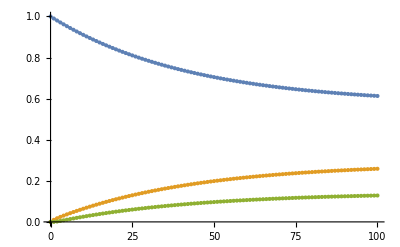

step size: 0.5

0.613523, 0.258212, 0.128265

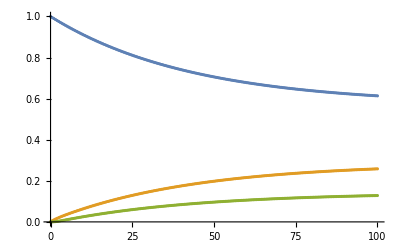

step size: 2

0.611812, 0.25933, 0.128858

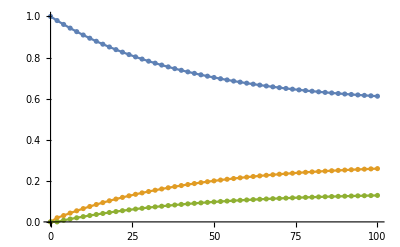

step size: 0.02

0.614068, 0.257856, 0.128076

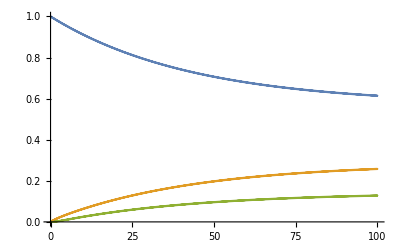

Combined plot:

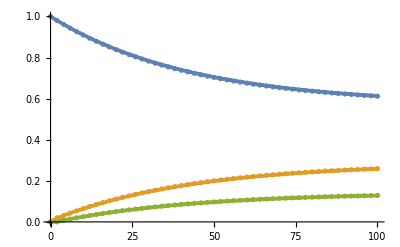

```mathematica
k1bi=0.02;
k2bi=0.4;

hi=1;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot1 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.5;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot2 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=2;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot3=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.02;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot4=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

Print["Combined plot: "]
Show[{plot1,plot2,plot3,plot4}]
```

```mathematica
analyticalSolAB= AseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolBB =BseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolCB =CseqB[100]/.{k1b->k1bi,k2b->k2bi}
```

0.614091

0.257841

0.128068

```mathematica
halvingFunction[x_]=0.5^x;

For[i=0,i<=10,i++,

hi=halvingFunction[i];
nStepsi=Round[time/hi];

Print["step size: ",hi];

Print["Concentrations of A,B,C, respectively, at t=100: "];
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];

Print["error in predicted concentrations of A,B,C, respectively: "];
Print[analyticalSolAB-AconcPrediction,", ", analyticalSolBB-BconcPrediction,", ",  analyticalSolCB-CconcPrediction];

Print["\n"];
]
```

step size: 1.

Concentrations of A,B,C, respectively, at t=100:

0.612954, 0.258584, 0.128462

error in predicted concentrations of A,B,C, respectively:

0.00113731, -0.000743053, -0.000394262

step size: 0.5

Concentrations of A,B,C, respectively, at t=100:

0.613523, 0.258212, 0.128265

error in predicted concentrations of A,B,C, respectively:

0.000568079, -0.000371149, -0.000196931

step size: 0.25

Concentrations of A,B,C, respectively, at t=100:

0.613807, 0.258027, 0.128166

error in predicted concentrations of A,B,C, respectively:

0.000283894, -0.000185479, -0.0000984148

step size: 0.125

Concentrations of A,B,C, respectively, at t=100:

0.613949, 0.257934, 0.128117

error in predicted concentrations of A,B,C, respectively:

0.00014191, -0.0000927156, -0.0000491947

step size: 0.0625

Concentrations of A,B,C, respectively, at t=100:

0.61402, 0.257887, 0.128092

error in predicted concentrations of A,B,C, respectively:

0.0000709459, -0.0000463518, -0.0000245942

step size: 0.03125

Concentrations of A,B,C, respectively, at t=100:

0.614056, 0.257864, 0.12808

error in predicted concentrations of A,B,C, respectively:

0.0000354707, -0.0000231744, -0.0000122963

step size: 0.015625

Concentrations of A,B,C, respectively, at t=100:

0.614073, 0.257853, 0.128074

error in predicted concentrations of A,B,C, respectively:

0.0000177348, -0.0000115868, -6.14794×10^-6

step size: 0.0078125

Concentrations of A,B,C, respectively, at t=100:

0.614082, 0.257847, 0.128071

error in predicted concentrations of A,B,C, respectively:

8.86724×10^-6, -5.79332×10^-6, -3.07392×10^-6

step size: 0.00390625

Concentrations of A,B,C, respectively, at t=100:

0.614087, 0.257844, 0.128069

error in predicted concentrations of A,B,C, respectively:

4.43358×10^-6, -2.89663×10^-6, -1.53695×10^-6

step size: 0.00195313

Concentrations of A,B,C, respectively, at t=100:

0.614089, 0.257843, 0.128068

error in predicted concentrations of A,B,C, respectively:

2.21678×10^-6, -1.44831×10^-6, -7.68471×10^-7

step size: 0.000976563

Concentrations of A,B,C, respectively, at t=100:

0.61409, 0.257842, 0.128068

error in predicted concentrations of A,B,C, respectively:

1.10839×10^-6, -7.24154×10^-7, -3.84235×10^-7

Similar to the previous run, we see that a step size of about h=0.03 would again be a good value. Actually, compared to the previous run, there is some additional leeway for a higher step size (maybe h=0.5). This is because for the step size of 0.0625, the largest error is about 0.0007 while in the previous run it was about 0.001 (for concentration of A).




Now in this next run we will test back reaction rates that are extremely small.

step size: 1

0.366982, 0.0207379, 0.61228

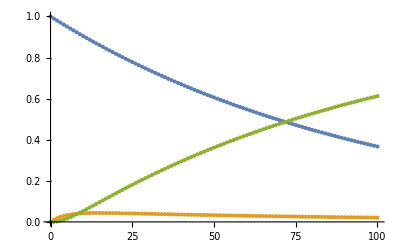

step size: 0.5

0.367905, 0.0207838, 0.611312

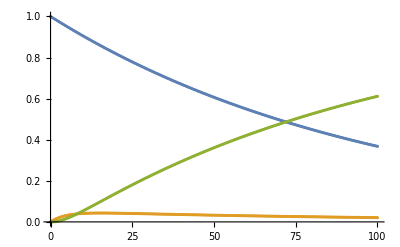

step size: 2

0.365124, 0.0206455, 0.61423

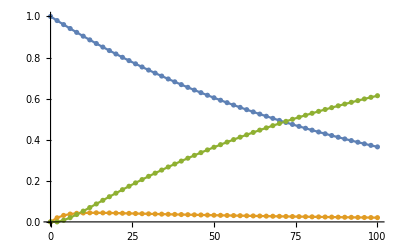

step size: 0.02

0.368787, 0.0208277, 0.610385

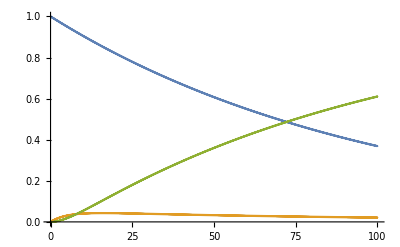

Combined plot:

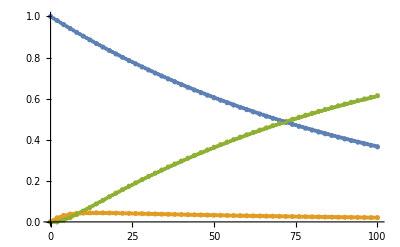

```mathematica
k1bi=0.0005;
k2bi=0.0005;

hi=1;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot1 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.5;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot2 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=2;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot3=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.02;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot4=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

Print["Combined plot: "]
Show[{plot1,plot2,plot3,plot4}]
```

```mathematica
analyticalSolAB= AseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolBB =BseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolCB =CseqB[100]/.{k1b->k1bi,k2b->k2bi}
```

0.368824

0.0208295

0.610347

```mathematica
halvingFunction[x_]=0.5^x;

For[i=0,i<=10,i++,

hi=halvingFunction[i];
nStepsi=Round[time/hi];

Print["step size: ",hi];

Print["Concentrations of A,B,C, respectively, at t=100: "];
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];

Print["error in predicted concentrations of A,B,C, respectively: "];
Print[analyticalSolAB-AconcPrediction,", ", analyticalSolBB-BconcPrediction,", ",  analyticalSolCB-CconcPrediction];

Print["\n"];
]
```

step size: 1.

Concentrations of A,B,C, respectively, at t=100:

0.366982, 0.0207379, 0.61228

error in predicted concentrations of A,B,C, respectively:

0.00184201, 0.0000916064, -0.00193362

step size: 0.5

Concentrations of A,B,C, respectively, at t=100:

0.367905, 0.0207838, 0.611312

error in predicted concentrations of A,B,C, respectively:

0.000919083, 0.0000457075, -0.00096479

step size: 0.25

Concentrations of A,B,C, respectively, at t=100:

0.368365, 0.0208067, 0.610829

error in predicted concentrations of A,B,C, respectively:

0.000459062, 0.0000228299, -0.000481892

step size: 0.125

Concentrations of A,B,C, respectively, at t=100:

0.368594, 0.0208181, 0.610588

error in predicted concentrations of A,B,C, respectively:

0.000229412, 0.000011409, -0.000240821

step size: 0.0625

Concentrations of A,B,C, respectively, at t=100:

0.368709, 0.0208238, 0.610467

error in predicted concentrations of A,B,C, respectively:

0.000114676, 5.70302×10^-6, -0.000120379

step size: 0.03125

Concentrations of A,B,C, respectively, at t=100:

0.368766, 0.0208266, 0.610407

error in predicted concentrations of A,B,C, respectively:

0.0000573305, 2.85114×10^-6, -0.0000601817

step size: 0.015625

Concentrations of A,B,C, respectively, at t=100:

0.368795, 0.0208281, 0.610377

error in predicted concentrations of A,B,C, respectively:

0.0000286634, 1.42548×10^-6, -0.0000300889

step size: 0.0078125

Concentrations of A,B,C, respectively, at t=100:

0.368809, 0.0208288, 0.610362

error in predicted concentrations of A,B,C, respectively:

0.0000143312, 7.12716×10^-7, -0.0000150439

step size: 0.00390625

Concentrations of A,B,C, respectively, at t=100:

0.368816, 0.0208291, 0.610354

error in predicted concentrations of A,B,C, respectively:

7.1655×10^-6, 3.56352×10^-7, -7.52185×10^-6

step size: 0.00195313

Concentrations of A,B,C, respectively, at t=100:

0.36882, 0.0208293, 0.610351

error in predicted concentrations of A,B,C, respectively:

3.58272×10^-6, 1.78175×10^-7, -3.7609×10^-6

step size: 0.000976563

Concentrations of A,B,C, respectively, at t=100:

0.368822, 0.0208294, 0.610349

error in predicted concentrations of A,B,C, respectively:

1.79135×10^-6, 8.90869×10^-8, -1.88044×10^-6

These results match the previous two runs pretty closely. A step size from h=0.03 to 0.06 would probably be a good choice.



For this final fun, we will try back reaction rate constants that are extremely large compared to the forward ones.

step size: 1

3733.76, -82105.1, 78372.4

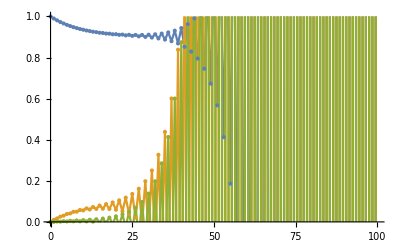

step size: 0.5

0.900904, 0.0900871, 0.00900869

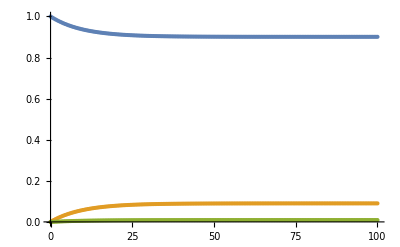

step size: 2

1.01346×10^22, -2.22913×10^23, 2.12779×10^23

-Graphics-

step size: 0.02

0.900905, 0.0900862, 0.0090086

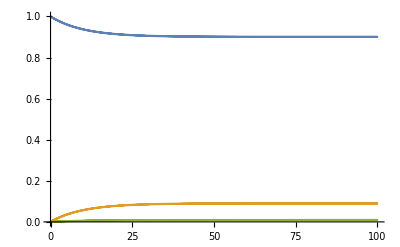

Combined plot:

-Graphics-

```mathematica
k1bi=0.1;
k2bi=2;

hi=1;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot1 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.5;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot2 =ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=2;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot3=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

hi=0.02;
nStepsi=Round[time/hi];
Print["step size: ", hi]
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];
plot4=ListPlot[{AData,BData,CData},PlotRange->{0,1},Joined->True,Mesh->All]

Print["Combined plot: "]
Show[{plot1,plot2,plot3,plot4}]
```

```mathematica
analyticalSolAB= AseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolBB =BseqB[100]/.{k1b->k1bi,k2b->k2bi}
analyticalSolCB =CseqB[100]/.{k1b->k1bi,k2b->k2bi}
```

0.900905

0.0900862

0.0090086

```mathematica
halvingFunction[x_]=0.5^x;

For[i=0,i<=10,i++,

hi=halvingFunction[i];
nStepsi=Round[time/hi];

Print["step size: ",hi];

Print["Concentrations of A,B,C, respectively, at t=100: "];
def[A0i,B0i,C0i,hi,k1i,k2i,k1bi,k2bi,nStepsi];

Print["error in predicted concentrations of A,B,C, respectively: "];
Print[analyticalSolAB-AconcPrediction,", ", analyticalSolBB-BconcPrediction,", ",  analyticalSolCB-CconcPrediction];

Print["\n"];
]
```

step size: 1.

Concentrations of A,B,C, respectively, at t=100:

3733.76, -82105.1, 78372.4

error in predicted concentrations of A,B,C, respectively:

-3732.86, 82105.2, -78372.4

step size: 0.5

Concentrations of A,B,C, respectively, at t=100:

0.900904, 0.0900871, 0.00900869

error in predicted concentrations of A,B,C, respectively:

9.86003×10^-7, -8.92076×10^-7, -9.39262×10^-8

step size: 0.25

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900867, 0.00900865

error in predicted concentrations of A,B,C, respectively:

5.16707×10^-7, -4.67486×10^-7, -4.92213×10^-8

step size: 0.125

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900864, 0.00900863

error in predicted concentrations of A,B,C, respectively:

2.64453×10^-7, -2.39261×10^-7, -2.51917×10^-8

step size: 0.0625

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900863, 0.00900861

error in predicted concentrations of A,B,C, respectively:

1.33773×10^-7, -1.2103×10^-7, -1.27431×10^-8

step size: 0.03125

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900863, 0.00900861

error in predicted concentrations of A,B,C, respectively:

6.72757×10^-8, -6.0867×10^-8, -6.40866×10^-9

step size: 0.015625

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900862, 0.0090086

error in predicted concentrations of A,B,C, respectively:

3.37355×10^-8, -3.05219×10^-8, -3.21363×10^-9

step size: 0.0078125

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900862, 0.0090086

error in predicted concentrations of A,B,C, respectively:

1.68922×10^-8, -1.52831×10^-8, -1.60915×10^-9

step size: 0.00390625

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900862, 0.0090086

error in predicted concentrations of A,B,C, respectively:

8.45223×10^-9, -7.64707×10^-9, -8.05156×10^-10

step size: 0.00195313

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900862, 0.0090086

error in predicted concentrations of A,B,C, respectively:

4.22765×10^-9, -3.82492×10^-9, -4.02724×10^-10

step size: 0.000976563

Concentrations of A,B,C, respectively, at t=100:

0.900905, 0.0900862, 0.0090086

error in predicted concentrations of A,B,C, respectively:

2.11421×10^-9, -1.91281×10^-9, -2.01398×10^-10

This is an odd result. A step size of 0.5 and below is giving approximations that are almost exactly equal to the analytical ones. But for step sizes 1 and 2, the numerical method for both the predicted concentration at t=100 and the overall plots are completely off.